This file computes and generates Figure 3 in the paper.
Define the CDF and PDF of utility distributions of agents A and B:

```mathematica
cdfa[x_]:=Piecewise[{{x*2,0≤x≤1/4},{1/2+2/3*(x-1/4),1/4≤x≤1},{1,x≥1}},0];
cdfb[x_]:=Piecewise[{{2/3*x,0≤x≤3/4},{1/2+2*(x-3/4),3/4≤x≤1},{1,x≥1}},0];
```

Define their PDFs:

```mathematica
pdfa[x_]=D[cdfa[y],y]/.{y->x}
pdfb[x_]=D[cdfb[y],y]/.{y->x}
```

Piecewise[{{0, x<0}, {2, 0<x<1/4}, {2/3, 1/4<x<1}, {0, x>1}, {Indeterminate, True}}]

Piecewise[{{0, x<0}, {2/3, 0<x<3/4}, {2, 3/4<x<1}, {0, x>1}, {Indeterminate, True}}]

Next, we solve for the quantile functions (i.e., inverses of the CDFs), which will allow us to sample from the distributions using inverse transform sampling

```mathematica
Solve[y==cdfa[x],x,Reals]
Solve[y==cdfb[x],x,Reals]
```

{{x→ConditionalExpression[y/2,0<y<1/2]},{x→ConditionalExpression[1/2 (-1+3 y),1/2<y<1]}}

{{x→ConditionalExpression[(3 y)/2,0<y<1/2]},{x→ConditionalExpression[(1+y)/2,1/2<y<1]}}

```mathematica
icdfa[y_]=Piecewise[{{y/2,0≤y≤1/2},{1/2*(3y-1),1/2≤y≤1}},Indeterminate]
icdfb[y_]=Piecewise[{{(3y)/2,0≤y≤1/2},{1/2*(1+y),1/2≤y≤1}},Indeterminate]
```

Piecewise[{{y/2, 0≤y≤1/2}, {1/2 (-1+3 y), 1/2≤y≤1}, {Indeterminate, True}}]

Piecewise[{{(3 y)/2, 0≤y≤1/2}, {(1+y)/2, 1/2≤y≤1}, {Indeterminate, True}}]

Verify that the quantile functions and CDFs match:

```mathematica
Reduce[icdfa[cdfa[x]]==x&&0≤x≤1,x]
Simplify[Reduce[cdfa[icdfa[x]]==x&&0≤x≤1,x]]
Reduce[icdfb[cdfb[x]]==x&&0≤x≤1,x]
Simplify[Reduce[cdfb[icdfb[x]]==x&&0≤x≤1,x]]
```

0≤x≤1

0≤x≤1

0≤x≤1

«1 more identical outputs»

Draw the utilities of 5000 random items:

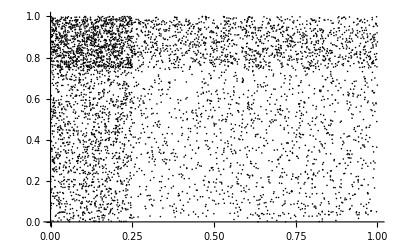

```mathematica
SeedRandom[0];
random=Table[{icdfa[RandomReal[]],icdfb[RandomReal[]]},{n,5000}];
itemutils=ListPlot[random,PlotStyle->Black]
```

Plot the region in which the maximum-percentile algorithm allocates to agent a: whenever CDF_A(utility_A) is larger than CDF_B(utility_B):

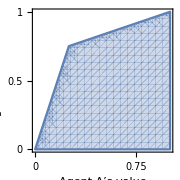

```mathematica
percentileregion=RegionPlot[cdfa[ua]≥cdfb[ub],{ua,0,1},{ub,0,1},Frame->True,PlotRangePadding->0,ImageSize->Small,FrameLabel->{"Agent A’s value","Agent B’s value"},FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,0.25,0.5,0.75,1},None}}]
```

Now, we compute the equalizing multipliers. Since there are only two agents, we can assume that agent B’s multiplier is one and only have to find a multiplier m for agent A such that agent A’s probability of receiving an item is 1/2 (which immediately implies that agent B’s probability is also 1/2):

```mathematica
pra[m_]=Integrate[pdfa[x]*cdfb[m*x],{x,0,1}]
```

Piecewise[{{m/4, 0≤m≤3/4}, {(-5+4 m)/(4 m), m>4}, {(1+4 m+m^2)/(12 m), 3<m<4}, {(-13+16 m+m^2)/(24 m), m==3}, {(-15+24 m+m^2)/(36 m), 1<m<3}, {(2+4 m+3 m^2)/(24 m), m==4}, {(9-24 m+25 m^2)/(36 m), 3/4<m≤1}, {0, True}}]

```mathematica
Solve[pra[m]==1/2,m,Reals]
N[%]
```

{{m→-3+2 √6}}

{{m→1.89898}}

We can now plot the region in which the multiplier algorithm allocates items to agent A, that is, where ma times agent A’s utility is larger than agent B’s utility:

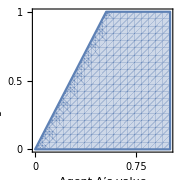

```mathematica
multiplierregion=RegionPlot[(-3+2 √6)*ua≥ub,{ua,0,1},{ub,0,1},Frame->True,PlotRangePadding->0,ImageSize->Small,FrameLabel->{"Agent A’s value","Agent B’s value"},FrameTicks->{{{0,0.25,0.5,0.75,1},None},{{0,0.25,0.5,0.75,1},None}}]
```

Finally, for the maximum-percentile figure, we want to highlight three items: two items given to agent A and with utilities as close to the median for both agents, and one item given to agent B with utilities at close to the top percentile for both agents:

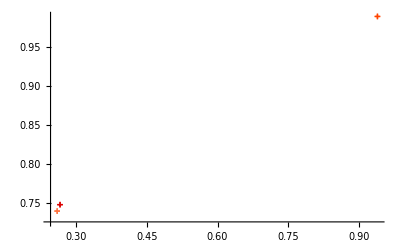

```mathematica
randomto1=Select[random,cdfa[#[[1]]]≥cdfb[#[[2]]] &];
randomto1s=SortBy[randomto1,(cdfa[#[[1]]]-1/2)^2+(cdfb[#[[2]]]-1/2)^2 &];
randomto2=Select[random,cdfa[#[[1]]]<cdfb[#[[2]]] &];
randomto2s=SortBy[randomto2,(cdfa[#[[1]]]-1)^2+(cdfb[#[[2]]]-1)^2 &];
cross=Graphics[{Thickness[.05],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}];
markers=ListPlot[{#}&/@Append[Take[randomto1s,2],randomto2s[[1]]],PlotMarkers->{cross,.1},PlotStyle->{ColorData[2][3],ColorData[2][1],ColorData[2][2]}]
```

Export the maximum-percentile panel of the figure to the current directory:

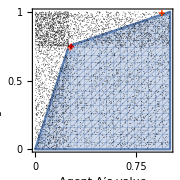

```mathematica
SetDirectory@NotebookDirectory[];
percentileplot=Show[{percentileregion,markers,itemutils}]
Export["percentile_plot1.pdf",percentileplot];
```

Export the multiplier panel of the figure:

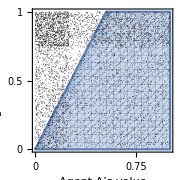

```mathematica
multiplierplot=Show[{multiplierregion,itemutils}]
Export["percentile_plot2.pdf",multiplierplot];
```